```mathematica
ClearAll["Global`*"];
```

```mathematica
m= 0.2 * 10 ^(-3);
S= 0.2 * 10^(-6);
a = 45;

vpn=v×cos(a °);
vkn=0.6×v×cos(a °);

ppn = -m *vpn;
pkn = m * vkn;
Δpn=pkn-ppn;
```

```mathematica
Fn=Δpn/Δt;
```

```mathematica
P=Fn/S;
```

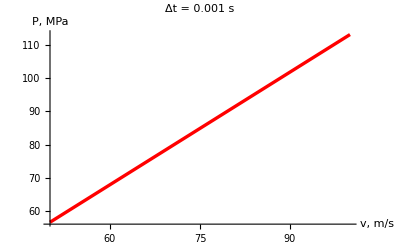

```mathematica
rys1=Plot[P×10^-6/.Δt->0.001,{v,50,100},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     Δt = 0.001 s    ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v, m/s","P,  MPa"}]
```

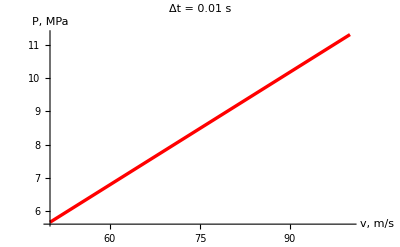

```mathematica
rys2=Plot[P×10^-6/.Δt->0.01,{v,50,100},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     Δt = 0.01 s    ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v, m/s","P,  MPa"}]
```